```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Desktop

```mathematica
chi2=Flatten[Import["./mub401/final/buffer/chi2.dat"]];
chi4=Flatten[Import["./mub401/final/buffer/chi4.dat"]];
r42=chi4/chi2;
```

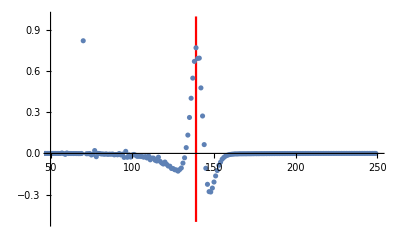

```mathematica
Show[ListLinePlot[{{139,-1},{139,1}},PlotRange->{{50,250},{-0.5,1}},PlotStyle->Red],ListPlot[r42[[1;;249]]-r42[[2;;250]],PlotRange->{{50,250},{-0.5,1}}]]
```

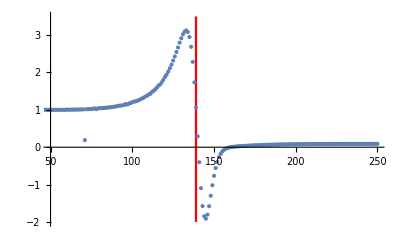

```mathematica
Show[ListLinePlot[{{139,-5},{139,5}},PlotRange->{{50,250},{-2,3.5}},PlotStyle->Red],ListPlot[r42,PlotRange->{{50,250},{-2,3.5}}]]
```